4 - 8 Critical points. Linearization.
Find the location and type of all critical points by linearization.

5.  y_1'=y_2
y_2'=-y_1+1/2 y_1^2

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[-Subscript[y, 1]+1/2 Subscript[y, 1]^2==0,Subscript[y, 1]]
```

{{y_1→0},{y_1→2}}

I will need the information contained in Table 4-1, p. 149 and Table 4-2, p. 150. In fact, because of their importance, I should put them in here, the first 4-1.

```mathematica
Grid[{{"Name","p=λ_1+λ_2","q=λ_1λ_2","Δ=(λ_1-λ_2)^2","Comments on λ_(1,) λ_2"},{"(a)Node","","q>0","Δ≥0","Real,same sign"},{"(b)Saddle point","","q<0","","Real,opposite signs"},{"(c)Center","p=0","q>0","","Pure imaginary"},{"(d)Spiral point","p≠0","","Δ<0","Complex, not pure imaginary"}},Frame->All]
```

Name | p=λ_1+λ_2 | q=λ_1λ_2 | Δ=(λ_1-λ_2)^2 | Comments on λ_(1,) λ_2
(a)Node |  | q>0 | Δ≥0 | Real,same sign
(b)Saddle point |  | q<0 |  | Real,opposite signs
(c)Center | p=0 | q>0 |  | Pure imaginary
(d)Spiral point | p≠0 |  | Δ<0 | Complex, not pure imaginary

followed by 4-2

```mathematica
Grid[{{"Type of Stability","p=λ_1+λ_2","q=λ_1λ_2"},{"(a)Stable and attractive","p<0","q>0"},{"(b)Stable","p≤0","q>0"},{"(c)Unstable","p>0 OR","OR q<0"}},Frame->All]
```

Type of Stability | p=λ_1+λ_2 | q=λ_1λ_2
(a)Stable and attractive | p<0 | q>0
(b)Stable | p≤0 | q>0
(c)Unstable | p>0 OR | OR q<0

So there will be two critical points, {0,0}, and {2,0}. First I look at {0,0}, with the eigensystem as

```mathematica
Eigensystem[{{0,1},{-1,0}}]
```

{{ⅈ,-ⅈ},{{-ⅈ,1},{ⅈ,1}}}

And manipulating the two eigenvalues to get p, q, and Δ

```mathematica
ev1=ⅈ
```

ⅈ

```mathematica
ev2=-ⅈ
```

-ⅈ

```mathematica
p=ev1+ev2
```

0

```mathematica
q=ev1 ev2
```

1

```mathematica
Δ=(ev1-ev2)^2
```

-4

And finding their fate in the grids,

This would be a stable center point. Equals text answer.

For the point (2,0)

```mathematica
Eigensystem[{{0,1},{1,0}}]
```

{{-1,1},{{-1,1},{1,1}}}

```mathematica
ev1=-1
```

-1

```mathematica
ev2=1
```

1

```mathematica
p=ev1+ev2
```

0

```mathematica
q=ev1 ev2
```

-1

```mathematica
Δ=(ev1-ev2)^2
```

4

And going to the grids with these,

This would be a unstable saddle point. Equals text answer.

7.  y_1'=-y_1+y_2-y_2^2
y_2'=-y_1-y_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[-Subscript[y, 1]-Subscript[y, 2]==0,Subscript[y, 2]]
```

{{y_2→-y_1}}

```mathematica
Solve[2 Subscript[y, 2]-Subscript[y, 2]^2==0,Subscript[y, 2]]
```

{{y_2→0},{y_2→2}}

This will give the set of points {0,0} and {-2,2},

(-1 | 1-2 y2
-1 | -1) is the general form of the Jacobian.  So starting with the first point {0,0}

```mathematica
Eigensystem[{{-1,1},{-1,-1}}]
```

{{-1+ⅈ,-1-ⅈ},{{-ⅈ,1},{ⅈ,1}}}

```mathematica
e1=-1+ⅈ
e2=-1-ⅈ
```

-1+ⅈ

-1-ⅈ

```mathematica
p==e1+e2
```

p==-2

```mathematica
q==e1 e2
```

q==2

```mathematica
Δ=(e1-e2)^2
```

-4

According to Tables 4-1 and 4-2, the critical point under consideration is a spiral point, and which is stable and attractive. p=-2, q=2, Δ=-4.

An interesting implication of the answer is that in finding critical points, the derivatives of all factors count.

Using the Jacobian system for the point (-2,2)

```mathematica
Eigensystem[{{-1,-3},{-1,-1}}]
```

{{-1-√3,-1+√3},{{√3,1},{-√3,1}}}

```mathematica
ev1=-1-√3
```

-1-√3

```mathematica
ev2=-1+√3
```

-1+√3

```mathematica
p=ev1+ev2
```

-2

```mathematica
q=ev1 ev2
```

```mathematica
(-1-√3) (-1+√3)//N
```

-2.

```mathematica
Δ=(ev1-ev2)^2
```

12

This would be a saddle point. Equals text answer. The text does not address stability, but 4-2 suggest unstable.

9 - 13 Critical points of ODEs
Find the location and type of all critical points by first converting the ODE to a system and then linearizing it.

9.  y''-9y+y^3=0

```mathematica
ClearAll["Global`*"]
```

Rearranging

```mathematica
y''=9 y - y^3
```

9 y-y^3

Making a substitution to get more things to work with

```mathematica
Subscript[y, 1]'=Subscript[y, 2]
```

y_2

I let y_1=y and then

```mathematica
Subscript[y, 2]'=9 Subscript[y, 1] - Subscript[y, 1]^3
```

9 y_1-y_1^3

```mathematica
Solve[9 Subscript[y, 1]-Subscript[y, 1]^3==0,Subscript[y, 1]]
```

{{y_1→-3},{y_1→0},{y_1→3}}

With the y_2 standing  by itself above, it will always be zero. So I have three points to consider: {-3,0}, {0,0}, {3,0}.

Stepping in here with the Jacobian system, the prototype matrix is (0 | 1
9-3 y1^2 | 0). So for the point (0,0),

```mathematica
Eigensystem[{{0,1},{9,0}}]
```

{{-3,3},{{-1,3},{1,3}}}

Eigenvalues not imaginary, but not equal.

```mathematica
e1=3 
e2=-3
```

3

-3

```mathematica
p=e1+e2
```

0

```mathematica
q=e1 e2
```

-9

```mathematica
Δ=(e1-e2)^2
```

36

So for the critical point (0,0) I have a saddle point by Table 4-1, and it is unstable by Table 4-2.

Again looking at the Jacobian system, the prototype matrix is (0 | 1
9-3 y1^2 | 0). So for the point (3,0),

```mathematica
Eigensystem[{{0,1},{-18,0}}]
```

{{3 ⅈ √2,-3 ⅈ √2},{{-ⅈ/(3 √2),1},{ⅈ/(3 √2),1}}}

```mathematica
ee1=3 ⅈ √2
```

3 ⅈ √2

```mathematica
ee2=-3 ⅈ √2
```

-3 ⅈ √2

```mathematica
p=Simplify[ee1 +ee2]
```

0

```mathematica
q=Simplify[ee1 ee2]
```

18

```mathematica
Δ=Simplify[(ee1-ee2)^2]
```

-72

This would be a center point. Agrees with text. The point (-3,0) would give the same results, also in agreement with the text. And with q<0 table 4-2 says these are unstable.

11.  y'' + Cos[y] = 0

```mathematica
ClearAll["Global`*"]
```

This problem is similar to Example 1 in Sec 4.5, where the sol’n is based on small angle formula for sin x≈x. Looking at the answer, it is seen that a peculiarity of the problem is that (0,0) is not a critical point, since cos x is not zero there. cos x equals zero at π/2 and multiples of it.

```mathematica
y''=-Cos[y]
```

-Cos[y]

```mathematica
y1'=y2
```

y2

```mathematica
y2'=-Cos[y1]
```

-Cos[y1]

Using the suggestion of the text answer,

y2'=-Cos[y1]=-Cos[±π/2+OverTilde[y1]]=Sin[±OverTilde[y1]]=±OverTilde[y1]

```mathematica
y2'=±OverTilde[y1]
```

±OverTilde[y1]

What is OverTilde[y1]? It is a point, something like (π/2,0). The second value (for y2) will be zero.

```mathematica
Eigensystem[{{0,1},{π/2,0}}]
```

{{-√(π/2),√(π/2)},{{-√(2/π),1},{√(2/π),1}}}

```mathematica
e1=-√(π/2)
```

-√(π/2)

```mathematica
e2=√(π/2)
```

√(π/2)

```mathematica
p=e1+e2
```

0

```mathematica
q=e1 e2
```

-π/2

```mathematica
Δ=(e1-e2)^2
```

2 π

So for the point OverTilde[y1]=(π/2,0) I get a saddle point, just as the text said.

```mathematica
Eigensystem[{{0,1},{-π/2,0}}]
```

{{ⅈ √(π/2),-ⅈ √(π/2)},{{-ⅈ √(2/π),1},{ⅈ √(2/π),1}}}

```mathematica
b1=ⅈ √(π/2)
```

ⅈ √(π/2)

```mathematica
b2=-ⅈ √(π/2)
```

-ⅈ √(π/2)

```mathematica
p=b1+b2
```

0

```mathematica
q=b1 b2
```

π/2

And for the point (-π/2,0) I get a center, again just as the text predicted.

```mathematica
Cos[π/2+x]==-Sin[x]
```

True

Checking what seemed reasonable.

```mathematica
TableForm[Table[{x,N[Sin[x],22]},{x,-.010000000000,.010000000000,0.001000000000}],32]
```

-0.01 | -0.00999983
-0.009 | -0.00899988
-0.008 | -0.00799991
-0.007 | -0.00699994
-0.006 | -0.00599996
-0.005 | -0.00499998
-0.004 | -0.00399999
-0.003 | -0.003
-0.002 | -0.002
-0.001 | -0.001
0. | 0.
0.001 | 0.001
0.002 | 0.002
0.003 | 0.003
0.004 | 0.00399999
0.005 | 0.00499998
0.006 | 0.00599996
0.007 | 0.00699994
0.008 | 0.00799991
0.009 | 0.00899988
0.01 | 0.00999983

Below is the answer for sin 0.001 which Mathematica is holding in memory:

```mathematica
0.0009999998333333408
```

This is still a approximation.

13.  y'' + Sin[y] = 0

```mathematica
ClearAll["Global`*"]
```

This one looks just like the last one.

```mathematica
y''=-Sin[y]
```

-Sin[y]

```mathematica
y1'=y2
```

y2

```mathematica
y2'=-Sin[y1]
```

The difference from the last problem may consist in the fact that sin is 0 at (0,0).

Trying to use the Jacobian approach, (0 | 1
-cos x | 0) would be the Jacobian standard matrix, I believe. So for x=±2n π, it should be

```mathematica
Eigensystem[{{0,1},{-1,0}}]
```

{{ⅈ,-ⅈ},{{-ⅈ,1},{ⅈ,1}}}

```mathematica
e1=ⅈ
```

ⅈ

```mathematica
e2=-ⅈ
```

-ⅈ

```mathematica
p=e1+e2
```

0

```mathematica
q=e1 e2
```

1

```mathematica
Δ=(e1-e2)^2
```

-4

This would be a center point, in agreement with the text.  For x=π±2 n π,

```mathematica
Eigensystem[{{0,1},{1,0}}]
```

{{-1,1},{{-1,1},{1,1}}}

This would be a saddle point, in agreement with the text. (p=0, q<0).

15. Trajectories. Write the ODE y''-4y+y^3=0 as a system, solve it for y_2 as a function of y_1, and sketch or graph some of the trajectories in the phase plane.

I do not follow the problem’s instructions to make a system.

```mathematica
eqn=y''[x]-4y[x]+y[x]^3==0
```

-4 y[x]+y[x]^3+y''[x]==0

```mathematica
sol=DSolve[eqn,y,x];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

The solution is complex, and fairly dense. There is some success in plotting (both halves of) the solution in regular x-y space.

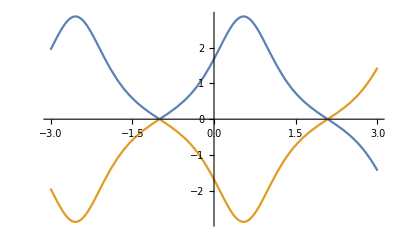

```mathematica
Plot[Evaluate[y[x]/.sol/.{C[1]->1,C[2]->1}],{x,-3,3},PlotRange->All]
```

Trying for phase space is not very successful. I am able to show one half of the solution, the ‘negative’ half. But it doesn’t look like the text, or like what I would expect.

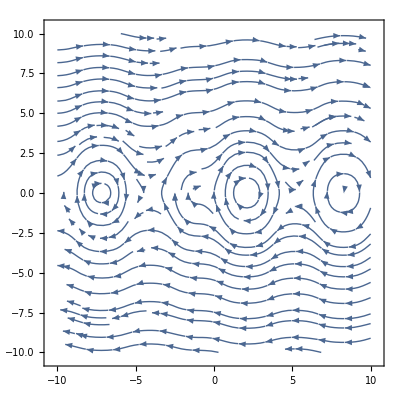

```mathematica
StreamPlot[{y,-3 ⅈ √(2/(-4+3 √2)) JacobiSN[(√(-4-3 √2-8 x-6 √2 x-4 x^2-3 √2 x^2))/(√2),(4-3 √2)/(4+3 √2)]+(4 ⅈ JacobiSN[(√(-4-3 √2-8 x-6 √2 x-4 x^2-3 √2 x^2))/(√2),(4-3 √2)/(4+3 √2)])/(√(-4+3 √2))},{x,-10,10},{y,-10,10},Frame->True]
```